```mathematica
SetDirectory[NotebookDirectory[]];
```

```mathematica
qPriorDist=TransformedDistribution[mG/mD,{mG\[Distributed]UniformDistribution[{0.6,10}],mD\[Distributed]UniformDistribution[{0.3,1.44}]}]
```

TransformedDistribution[x1/x2,{x1\[Distributed]UniformDistribution[{0.6,10}],x2\[Distributed]UniformDistribution[{0.3,1.44}]}]

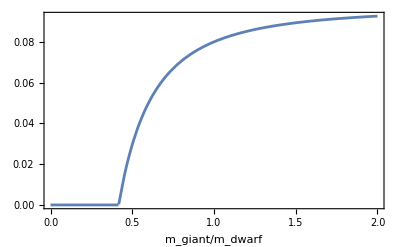

```mathematica
plt1=Plot[PDF[qPriorDist,x],{x,0,2},Frame->{{True,False},{True,False}},FrameLabel->{"m_giant/m_dwarf", ""}]
```

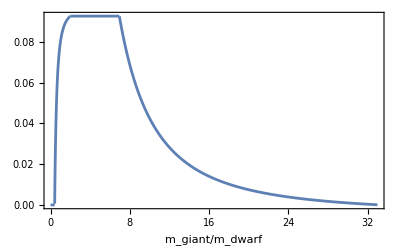

```mathematica
plt2=Plot[PDF[qPriorDist,x],{x,0,33},Frame->{{True,False},{True,False}},FrameLabel->{"m_giant/m_dwarf", ""},PlotPoints->400]
```

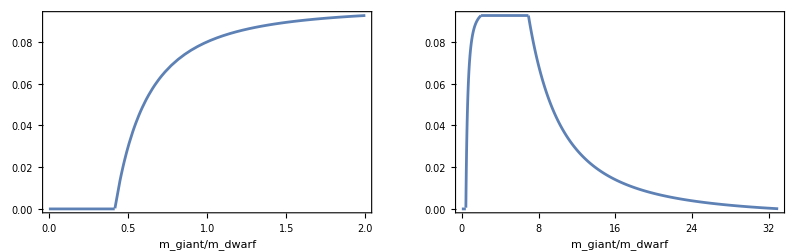
PDF отношения равномерных случайных величин
-Graphics-

```mathematica
qPriorPlot=Column[{Style["PDF отношения равномерных случайных величин","Author"],GraphicsRow[{plt1,plt2}]},Center]
```

```mathematica
Export["q_prior.pdf",qPriorPlot]
```

q_prior.pdf